```mathematica
ClearAll["Global`*"];
```

```mathematica
ns1={25,50,100,250,500,1000,5000};
ns5={25,50,100,250};
e1={0.0009366602775,0.0005210139857,0.0002662051776,0.0001073022709,0.00005373974536,0.00002688748609,0.000005379873};
e5={0.00004333083477,0.0000008496817301,0.00000007265136004,0.000000001922590087};

set1=Thread[{ns1,e1}];
set5=Thread[{ns5,e5}];
```

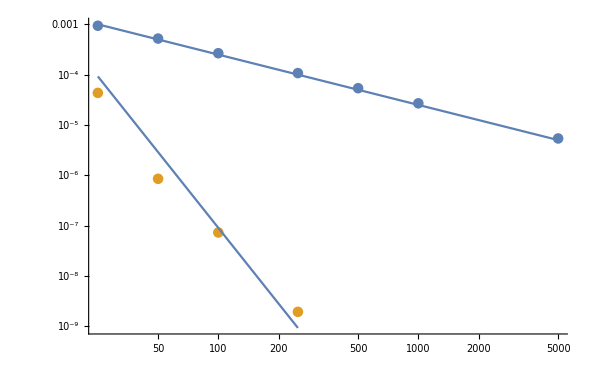

```mathematica
Show[ListLogLogPlot[{set1,set5},PlotRange->All],LogLogPlot[0.025 x^-1,{x,25,5000}],LogLogPlot[900.25 x^-5,{x,25,250}],PlotRange->All]
```

```mathematica
OutAll=Flatten[{{{"ColumnX","ColumnY"}},set5},1];
SetDirectory[NotebookDirectory[]];
Export["anand-data/WENO5-Errors.csv",OutAll,"Table"];
```